### 2nd deriv of gauss

2nd deriv of Gauss

ⅇ^(-x^2) (-2+4 x^2)

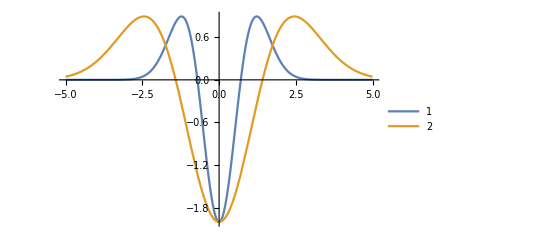

```mathematica
D[E^(-x^2),{x,2}]//Simplify
ricker =%;
Plot[{ricker,(ricker/.{x-> x/2}//Evaluate)},{x,-5,5},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
Integrate[ricker*ricker,{x,-10,10}]//N
```

3.75994

```mathematica
Table[Integrate[ricker*x^m,{x,-10,10}],{m,0,2}]//N//Chop
```

{0,0,3.54491}

the 2nd deriv of Ricker has up to m=0, 1 vanish_mom

```mathematica
Table[Integrate[(ricker/.{x->(x-1.45)/2.5})*x^m,{x,-20,20}],{m,0,2}]//N//Chop
```

{0,0,55.3892}

```mathematica
Table[Integrate[(ricker/.{x->(x)/RandomReal[]})*x^m,{x,-20,20}],{m,0,2}]//N//Chop
```

{0,0,0.00438681}

still vanish_mom when have j &k (continuous fine)

### 4th deriv of gauss

4 ⅇ^(-x^2) (3-12 x^2+4 x^4)

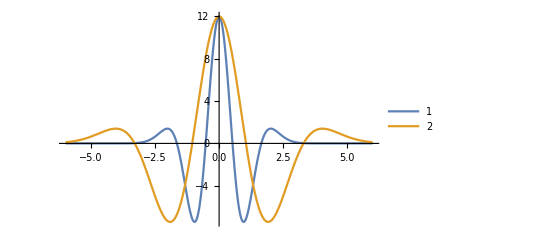

```mathematica
D[E^(-x^2),{x,4}]//Simplify
ricker =%;
Plot[{ricker,(ricker/.{x-> x/2}//Evaluate)},{x,-6,6},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
Table[Integrate[ricker*x^m,{x,-10,10}],{m,0,4}]//N//Chop
```

{0,0,0,0,42.5389}

the 4th deriv of Ricker has up to m=0, 1,2,3  vanish_mom

```mathematica
Table[Integrate[(ricker/.{x->(x-1.45)/2.5})*x^m,{x,-20,20}],{m,0,4}]//N//Chop
```

{0,0,0,0,4154.19}

```mathematica
Table[Integrate[(ricker/.{x->(x)/RandomReal[]})*x^m,{x,-20,20}],{m,0,4}]//N//Chop
```

{0,0,0,0,0.0000270181}

still vanish_mom when have j &k (continuous fine)

## 2nd: make σ,τ to target T_i and T_f

focus on 2nd deriv

ⅇ^(-x^2) (-2+4 x^2)

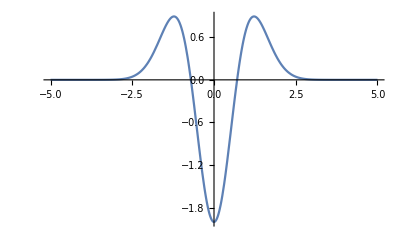

```mathematica
D[E^(-x^2),{x,2}]//Simplify
ricker =%;
Plot[{ricker},{x,-5,5},PlotRange->Full,PlotLegends->Automatic]
```

the range is around (-3, 3) with center 0.
if we want the range is from [T_i,  T_f], then what we should do is ,
before doing j,k tranformation make x ==> (x-τ)/σ

```mathematica
Solve[(Ti-τ)/σ==-3  &&(Tf-τ)/σ==3,{τ,σ}]
```

{{τ→(Tf+Ti)/2,σ→(Tf-Ti)/6}}

```mathematica
myRicker [j_,k_,Ti_,Tf_]:=(D[E^(-x^2),{x,2}]/.{x-> ((x-(Tf+Ti)/2)/((Tf-Ti)/6) -k)*2^j})
```

-2 ⅇ^(-9/25 (-5+x)^2)+36/25 ⅇ^(-9/25 (-5+x)^2) (-5+x)^2

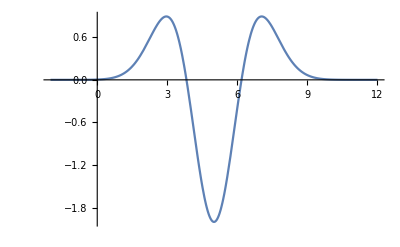

```mathematica
myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]
Plot[%,{x,-2,12},PlotRange->Full]
```

```mathematica
NIntegrate[myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10],{x,-15,15}]
```

6.26657

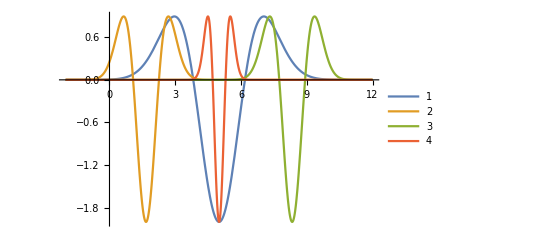

```mathematica
Plot[{myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)1,(*k*)-2, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)1,(*k*)2, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)2,(*k*)0, (*Ti*)0,(*Tf*)10]//Evaluate
 },
{x,-2,12},PlotRange->Full,PlotLegends->Automatic]
```

General::munfl: Exp[-5183.6] is too small to represent as a normalized machine number; precision may be lost.

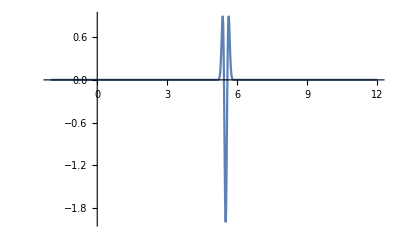

```mathematica
Plot[myRicker[(*j*)4,(*k*)0.3, (*Ti*)0,(*Tf*)10]//Evaluate,{x,-2,12},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]/.{x-> 10/2}
```

-2

```mathematica
myRicker [j_,k_,Ti_,Tf_]:=(D[E^(-x^2),{x,2}]/.{x-> ((x-(Tf+Ti)/2)/((Tf-Ti)/6) -k)*2^j})
```

如果说，当x=(Tf-Ti)/2 = 5的时候，(j=0, k=0)的curve 处在最低点 -2 
那么我们现在让j变成非0⃣️的 一个     值，k取多少， x

Look at the curve (j=0,k=0) and when x=(Tf-Ti)/2 =5 =x0, the point is at the y_min=-2.  x_min=5
Now if we change (jk), the shape of curve scale and position shift.  
The question is if we want the x_min to move to x1, what the k value should be, for a given j ?
first of all, we define  (Tf+Ti)/2 = M and (Tf-Ti)/6=D
the 1st case give (x0-M)/D
the 2nd case givs [(x1-M)/D-k]/2^j, and we want these to to be equal

```mathematica
Solve[(x0-M)/DD == ((x1-M)/DD -k)*2^j,{k}]//FullSimplify
```

{{k→(2^-j (M-2^j M-x0+2^j x1))/DD}}

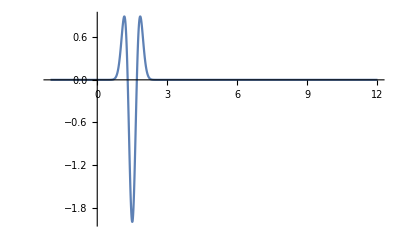

```mathematica
Tf=10;Ti=0;
M=(10+0)/2; DD = (10-0)/6; x0=(10-0)/2;
x1=1.5(*we want the position of new nadia*); 
j=Log[6]/Log[2];
Plot[myRicker[(*j*)j,(*k*)(2^-j (M-2^j M-x0+2^j x1))/DD, (*Ti*)Ti,(*Tf*)Tf]//Evaluate,{x,-2,12},PlotRange->Full,PlotLegends->Automatic]

Clear[x1,M,DD,x0,j,Tf,Ti]
```

In this way, we know how to set the new k for a given j, x1  (we assume Tf Ti fixed always, so x0  DD MM)
k = 2^-j (M-2^j M-x0+2^j x1)/DD 
好的

```mathematica
NIntegrate[myRicker[(*j=*)0,(*k=*)0,(*Ti*)0,(*Tf*)10]
myRicker[(*j=*)2,(*k=*)3,(*Ti*)0,(*Tf*)10],{x,-20,10}]
```

0.00712961

## 4th: make σ,τ to target T_i and T_f

focus on 2nd deriv

```mathematica
1/(2π)D[E^(-x^2),{x,4}]//Simplify
```

(ⅇ^(-x^2) (6-24 x^2+8 x^4))/π

4 ⅇ^(-x^2) (3-12 x^2+4 x^4)

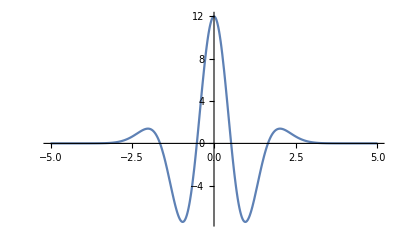

```mathematica
D[E^(-x^2),{x,4}]//Simplify
ricker =%;
Plot[{ricker},{x,-5,5},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
(*check vanishing moment*)
Table[NIntegrate[ricker*x^m,{x,-10,10}]//Chop,{m,0,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.917813}. NIntegrate obtained -1.06581×10^-14 and 1.45468×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.11313}. NIntegrate obtained -1.77636×10^-15 and 2.7378×10^-15 for the integral and error estimates.

{0,0,0,0,42.5389,0}

the range is around (-3, 3) with center 0.
if we want the range is from [T_i,  T_f], then what we should do is ,
before doing j,k tranformation make x ==> (x-τ)/σ

```mathematica
Solve[(Ti-τ)/σ==-3  &&(Tf-τ)/σ==3,{τ,σ}]
```

{{τ→(Tf+Ti)/2,σ→(Tf-Ti)/6}}

```mathematica
myRicker [j_,k_,Ti_,Tf_]:=1/(2π)(D[E^(-x^2),{x,4}]/.{x-> ((x-(Tf+Ti)/2)/((Tf-Ti)/6) -k)*2^j})
```

(12 ⅇ^(-9/25 (-5+x)^2)-432/25 ⅇ^(-9/25 (-5+x)^2) (-5+x)^2+1296/625 ⅇ^(-9/25 (-5+x)^2) (-5+x)^4)/(2 π)

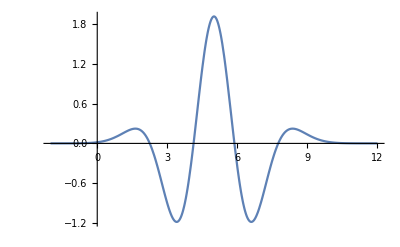

```mathematica
myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]
Plot[%,{x,-2,12},PlotRange->Full]
```

```mathematica
NIntegrate[myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10],{x,-15,15}]
```

5.55569

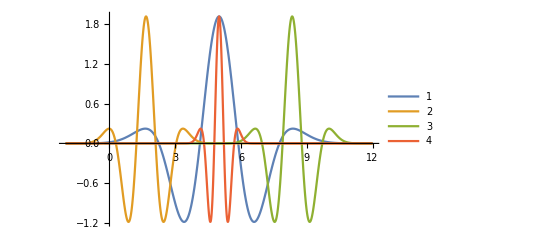

```mathematica
Plot[{myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)1,(*k*)-2, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)1,(*k*)2, (*Ti*)0,(*Tf*)10]//Evaluate,
myRicker[(*j*)2,(*k*)0, (*Ti*)0,(*Tf*)10]//Evaluate
 },
{x,-2,12},PlotRange->Full,PlotLegends->Automatic]
```

General::munfl: Exp[-5183.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

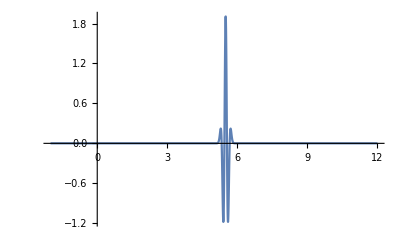

```mathematica
Plot[myRicker[(*j*)4,(*k*)0.3, (*Ti*)0,(*Tf*)10]//Evaluate,{x,-2,12},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
myRicker[(*j*)0,(*k*)0, (*Ti*)0,(*Tf*)10]/.{x-> 10/2}
```

6/π

```mathematica
myRicker [j_,k_,Ti_,Tf_]:=1/(2π)(D[E^(-x^2),{x,4}]/.{x-> ((x-(Tf+Ti)/2)/((Tf-Ti)/6) -k)*2^j})
```

如果说，当x=(Tf-Ti)/2 = 5的时候，(j=0, k=0)的curve 处在最低/高点 -2 
那么我们现在让j变成非0⃣️的 一个     值，k取多少， x

Look at the curve (j=0,k=0) and when x=(Tf-Ti)/2 =5 =x0, the point is at the y_min=-2.  x_min=5
Now if we change (jk), the shape of curve scale and position shift.  
The question is if we want the x_min to move to x1, what the k value should be, for a given j ?
first of all, we define  (Tf+Ti)/2 = M and (Tf-Ti)/6=D
the 1st case give (x0-M)/D
the 2nd case givs [(x1-M)/D-k]/2^j, and we want these to to be equal

```mathematica
Solve[(x0-M)/DD == ((x1-M)/DD -k)*2^j,{k}]//FullSimplify
```

{{k→(2^-j (M-2^j M-x0+2^j x1))/DD}}

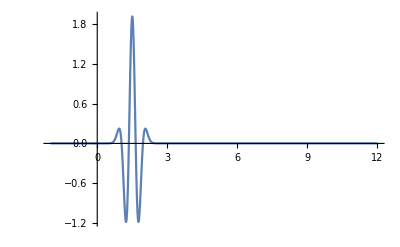

```mathematica
Tf=10;Ti=0;
M=(10+0)/2; DD = (10-0)/6; x0=(10-0)/2;
x1=1.5(*we want the position of new nadia*); 
j=Log[6]/Log[2];
Plot[myRicker[(*j*)j,(*k*)(2^-j (M-2^j M-x0+2^j x1))/DD, (*Ti*)Ti,(*Tf*)Tf]//Evaluate,{x,-2,12},PlotRange->Full,PlotLegends->Automatic]

Clear[x1,M,DD,x0,j,Tf,Ti]
```

In this way, we know how to set the new k for a given j, x1  (we assume Tf Ti fixed always, so x0  DD MM)
k = 2^-j (M-2^j M-x0+2^j x1)/DD 
好的

```mathematica
NIntegrate[myRicker[(*j=*)0,(*k=*)0,(*Ti*)0,(*Tf*)10]
myRicker[(*j=*)2,(*k=*)3,(*Ti*)0,(*Tf*)10],{x,-20,10}]
```

-0.00205453